# An Experience Binarization and validation using ODE simulation of an artificial Boolean network Model

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Booned`
```

```mathematica
<<Bi4Back`
```

```mathematica
<<Functionsneededpackage`
```

```mathematica
Unprotect[t];Clear[t];Protect[t];
```

## RESEAU BOOLEEN EXEMPLE

```mathematica
FB={x1->x4&&x3&&x5,
x2->x1,
x3->!x2,
x4->x2,
x5->x3&&!x4}
```

{x1→x4&&x3&&x5,x2→x1,x3→!x2,x4→x2,x5→x3&&!x4}

```mathematica
FindEquilibria@ModelOf[FB]
```

{{{x1→False,x2→False,x3→True,x4→False,x5→True}}}

```mathematica
StableFB=Association/@StableStates[FB]
```

{<|x1→False,x2→False,x3→True,x4→False,x5→True|>}

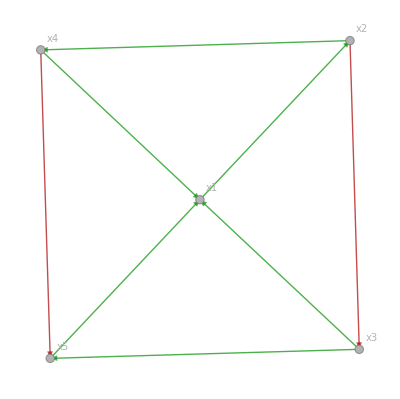

```mathematica
IG=NiceIG[InteractionGraphSimple[FB]]
```

## SIMULATION

```mathematica
name="Artifitial model"
```

Artifitial model

### Parameters

Expression rate

```mathematica
κ=<|x1->4,x2->2,x3->3,x4->1,x5->4|>
```

<|x1→4,x2→2,x3→3,x4→1,x5→4|>

Degradation rate

```mathematica
γ=AssociationThread[Keys[FB],0.5]
```

<|x1→0.5,x2→0.5,x3→0.5,x4→0.5,x5→0.5|>

Threshold for being activated or inhibited.

```mathematica
(*θ=Thresholding[Keys[FB],0.5,0.20]*)
```

```mathematica
θ=<|x1->0.6,x2->0.7,x3->0.6,x4->0.6,x5->0.4|>
```

<|x1→0.6,x2→0.7,x3→0.6,x4→0.6,x5→0.4|>

```mathematica
Highlighted[TableForm[{Mean[θ],StandardDeviation[θ]}]]
```

0.58
0.109545

### For a stable state

```mathematica
stablestate=StableFB[[1]]
```

<|x1→False,x2→False,x3→True,x4→False,x5→True|>

```mathematica
initialcondition=<|x1->4,x2->5,x3->8,x4->0.5,x5->7|>
```

<|x1→4,x2→5,x3→8,x4→0.5,x5→7|>

```mathematica
FindEquilibria@ModelOf[FB]
```

{{{x1→False,x2→False,x3→True,x4→False,x5→True}}}

#### ODE

```mathematica
system={{x1'[t]==4 hillp[x3[t],0.6] hillp[x4[t],0.6] hillp[x5[t],0.4]-0.5 x1[t]}, {x1[0]==4}, {x2'[t]==2 hillp[x1[t],0.6]-0.5 x2[t]}, {x2[0]==5}, {x3'[t]==3 hillm[x2[t],0.7]-0.5 x3[t]}, {x3[0]==8}, {x4'[t]==hillp[x2[t],0.7]-0.5 x4[t]}, {x4[0]==0.5}, {x5'[t]==4 hillm[x4[t],0.6] hillp[x3[t],0.6]-0.5 x5[t]}, {x5[0]==7}}
```

{{x1'[t]==4 hillp[x3[t],0.6] hillp[x4[t],0.6] hillp[x5[t],0.4]-0.5 x1[t]},{x1[0]==4},{x2'[t]==2 hillp[x1[t],0.6]-0.5 x2[t]},{x2[0]==5},{x3'[t]==3 hillm[x2[t],0.7]-0.5 x3[t]},{x3[0]==8},{x4'[t]==hillp[x2[t],0.7]-0.5 x4[t]},{x4[0]==0.5},{x5'[t]==4 hillm[x4[t],0.6] hillp[x3[t],0.6]-0.5 x5[t]},{x5[0]==7}}

#### Experiments

```mathematica
EXP=ThreeExperienceFromODE[FB,system,40,stablestate,θ] (*voir la fonction dans le package functionsneeded*)
```

<|16.3→<|x1→0.0329,x2→0.197,x3→4.31,x4→0.563,x5→0.5|>,28.13→<|x1→0,x2→0.000532,x3→6.,x4→0.00152,x5→7.98|>,40.→<|x1→0,x2→0,x3→6.,x4→0,x5→8.|>|>

```mathematica
Epil=Keys[EXP]
```

{16.3,28.13,40.}

```mathematica
fun=#[t]&/@Keys[FB];
```

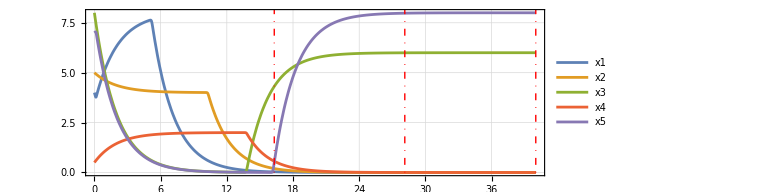

```mathematica
Fig1=Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,40}]],{t,0,40}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel-> "", ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{Epil[[1]],0},{Epil[[1]],10}}] ,Line[{{Epil[[2]],0},{Epil[[2]],10}}], Line[{{Epil[[3]],0},{Epil[[3]],10}}]}]
```

```mathematica
result=ThreeExperimentsBinarisation[IG,Values[EXP] , stablestate] (*voir la fonction dans le package functionsneeded*)
```

{<|x1→False,x2→False,x3→True,x4→False,x5→True|>,<|x1→False,x2→False,x3→True,x4→False,x5→True|>,<|x1→False,x2→False,x3→True,x4→False,x5→True|>}

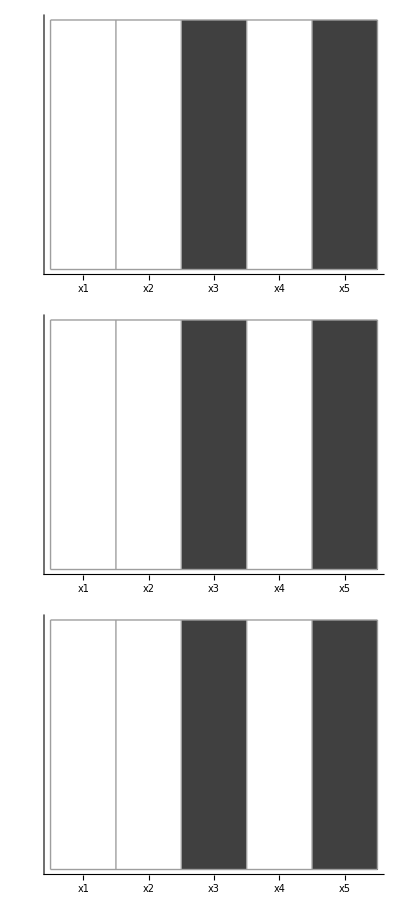

```mathematica
TableForm[Function[profile, ArrayPlot[{Values[profile]}, ColorRules->{True -> GrayLevel[0.25],False->White},Mesh->All, ImageSize->Large,
Axes->{True,False}, Ticks->{Thread[{Range[0.5,Length[profile]-0.5,1],Keys[profile]}],None}]]/@result]
```

```mathematica
dis=Distanceofdissimilarity[result,stablestate] (*voir la fonction dans le package functionsneeded*)
```

{0,0,0}